## GenerateBoundaryLayer-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51a (07 June 2017)) loaded Thu 8 Jun 2017 14:23:59
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

Generate 50 random vertices to use a Voronoi Centers

```mathematica
r:=RandomReal[{0,100}]; 
v=Table[{r,r}, {50}]
```

{{62.8244,96.2686},{76.0783,64.4959},{31.7338,50.9633},{23.0468,18.7997},{38.2032,11.4493},{16.4384,16.861},{33.5239,57.1033},{75.7114,90.5363},{90.5208,83.0416},{66.1223,48.5783},{39.2261,82.2089},{39.722,10.778},{42.1653,5.50876},{11.1263,4.36872},{24.0407,18.8239},{30.1751,6.40737},{97.7052,81.6775},{79.237,12.5781},{64.7335,72.9485},{42.3226,54.1976},{62.8394,4.62995},{99.6687,40.0814},{48.0536,69.5125},{64.8642,6.79913},{29.2041,92.0678},{68.7329,63.0833},{73.06,58.4656},{93.9102,76.821},{45.6161,3.67611},{52.332,88.6435},{53.8687,31.8556},{60.382,7.33014},{30.1933,62.6929},{95.2641,60.58},{49.2077,15.5189},{72.044,66.9211},{85.5772,33.8895},{27.5603,89.9097},{24.7489,40.3995},{91.7259,93.6565},{49.7354,5.04717},{98.1456,67.3216},{25.946,51.081},{15.5625,74.3246},{9.04451,8.35277},{1.80725,15.908},{5.0862,27.5397},{41.9653,91.9761},{36.8985,75.2013},{22.3111,60.554}}

```mathematica
bl=GenerateBoundaryLayer[v]
```

{{-8.46094,39.7452},{-11.4617,25.913},{-14.3945,12.2161},{-8.32512,4.5317},{-2.29101,-2.98448},{3.81237,-10.5522},{14.4371,-10.9996},{24.7491,-11.6657},{35.4074,-12.2438},{45.9089,-12.9384},{56.6069,-12.0355},{67.0042,-11.4567},{74.7723,-7.77392},{82.2176,-3.83004},{89.8349,-0.220768},{96.1728,8.57792},{102.792,17.4571},{109.081,26.5122},{115.564,35.2362},{115.134,48.0414},{114.713,60.5403},{114.139,73.27},{113.785,85.8702},{109.625,93.0895},{105.431,100.126},{101.095,107.381},{88.2093,109.282},{75.2993,111.213},{62.5405,112.883},{52.08,111.28},{41.6493,109.818},{31.2794,108.207},{20.95,106.49},{14.0564,97.9837},{7.21451,89.8126},{0.552018,81.4529},{-2.53567,67.6871},{-5.5243,53.6974}}

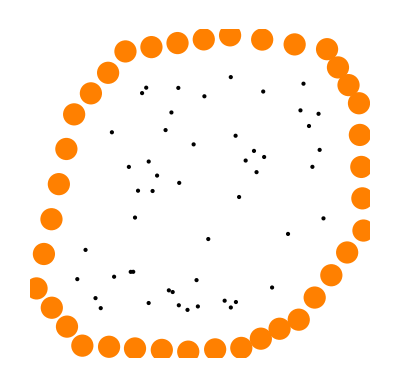

```mathematica
Graphics[{Point[v], Orange, PointSize[.04], Point[bl]}]
```

Use the Voronoi Centers to generate a tissue with 50 cells using the Bounded-Cell-Voronoi algorithm

```mathematica
w=BoundedCellVoronoi[v];
```

Show the tissue, original Voronoi Centers, and artificial Boundary Layer centers.

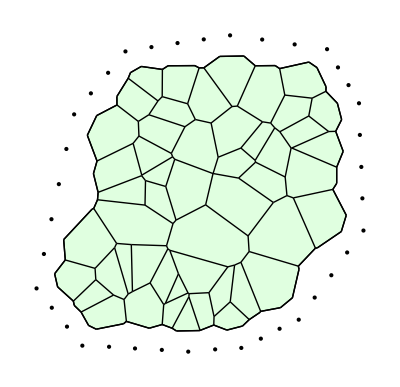

```mathematica
Show[ShowTissue[w], 
Graphics[Point[bl]]]
```

```mathematica
bcv=BoundedCellVoronoi[Join[v,bl]];
```

```mathematica
COB = CellsOnBoundary[bcv]
```

{51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88}

```mathematica
cc=If[MemberQ[COB,#], LightBlue, Pink]&/@Range[NTissueCells[bcv]];
```

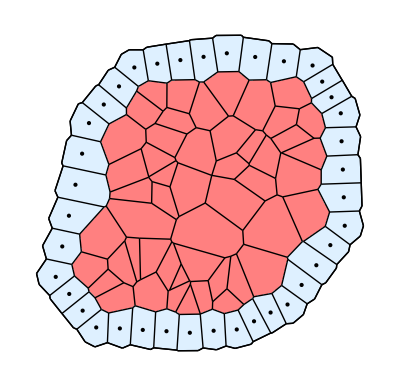

```mathematica
ShowTissue[bcv, "CellStyles"-> cc, Epilog-> Point[bl]]
```